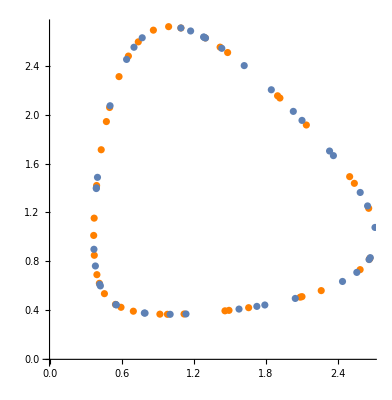

0.00163134

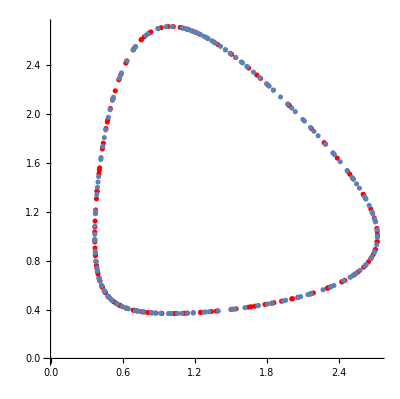

0.000181075

```mathematica
t1 = 0.3; t2 = t1 + 4;
y1[t_]:=Exp[Sin[t^2]]; y2[t_]:= Exp[Cos[t^2]];
SetDirectory["D:\\BMSTU\\5th_term\\4 semestr\\Rodin\\DZ\\DZ\\programm"];
datRK= Import["RK4.dat"];
datDP= Import["DP4_5.dat"];

listRK= {};
For[i = 1, i <= Length[datRK]-1, ++i,
AppendTo[listRK, {datRK[[i,2]], datRK[[i,3]]}]]
listDP= {};
For[i = 1, i <= Length[datDP]-1, ++i,
AppendTo[listDP, {datDP[[i,2]], datDP[[i,3]]}]]

listRKA = {};
tau = 4/(Length[listRK]-1);
For[ t= 0.3, t <= 4.3, t+=tau,
AppendTo[listRKA, {y1[t], y2[t]}]]
listRKAC= {};
For[i = 1, i <= Length[listRK], ++i,
AppendTo[listRKAC, {y1[datRK[[i,1]]], y2[datRK[[i,1]]]}]]
listDPA = {};
tau = 4/(Length[listDP]-1);
For[ t= 0.3, t <= 4.3, t+=tau,
AppendTo[listDPA, {y1[t], y2[t]}]]
listDPAC= {};
For[i = 1, i <= Length[listDP], ++i,
AppendTo[listDPAC, {y1[datDP[[i,1]]], y2[datDP[[i,1]]]}]]

LRK= ListPlot[listRK, PlotStyle->Orange, AspectRatio->Automatic];
LDP= ListPlot[listDP, PlotStyle->Red, AspectRatio->Automatic];
LRKA= ListPlot[listRKA , AspectRatio->Automatic];
LDPA= ListPlot[listDPA, AspectRatio->Automatic];
Show[LRK, LRKA]
Norm[listRK - listRKAC]
Show[LDP, LDPA]
Norm[listDP - listDPAC]
```

```mathematica
listRK //Length
listRKA // Length
listRKAC // Length
```

40

40

40

```mathematica
listDP//Length
listDPA // Length
listDPAC // Length
```

164

164

164